```mathematica
Psi[theta_,d_,n1_,n2_]:=4 Pi d Cos[theta]*n1+2 ArcTan[(n1/n2) Sqrt[((n1/n2)^2-1) Tan[theta]^2-1]]+2 ArcTan[n1 Sqrt[(n1^2-1) Tan[theta]^2-1]]
```

```mathematica
Psi2[theta_,d_,n1_,n2_]:=4 Pi d Cos[theta]*n1+2 ArcTan[(n2/n1) Sqrt[((n1/n2)^2-1) Tan[theta]^2-1]]+2 ArcTan[n1^-1 Sqrt[(n1^2-1) Tan[theta]^2-1]]
```

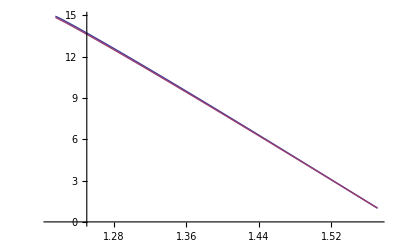

```mathematica
Plot[{Psi[x,13,1.6,1.5]/2/Pi,Psi2[x,13,1.6,1.5]/2/Pi},{x,1.21,Pi/2}]
```